```mathematica
dampingng[ω_, vth_, k_,κ_]:= ω*Sqrt[Pi]*ω^3/k^3* (-1-κ)/(vth^3(-1/2+κ)^(3/2))*(1+(ω^2/(k^2 vth^2)+ 1.5)/(κ-1/2))^(-2-κ)
```

```mathematica
(dampingng[#, 1, 1,3]&)/@{0.01,0.1,1,10,100}
```

{-1.71029×10^-9,-0.0000168929,-0.0560499,-0.000143965,-1.74806×10^-10}

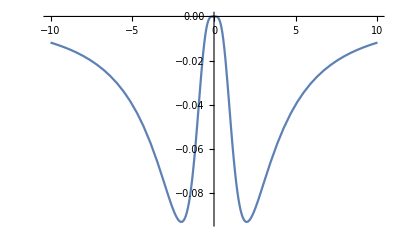

```mathematica
Plot[dampingng[ω, 1, 1,1], {ω,-10,10}]
```